```mathematica
Table[{n,LegendreP[n,z],√((2n+1)/2)LegendreP[n,z]},{n,0,10}]//TableForm
```

0 | 1 | 1/(√2)
1 | z | √(3/2) z
2 | 1/2 (-1+3 z^2) | 1/2 √(5/2) (-1+3 z^2)
3 | 1/2 (-3 z+5 z^3) | 1/2 √(7/2) (-3 z+5 z^3)
4 | 1/8 (3-30 z^2+35 z^4) | (3 (3-30 z^2+35 z^4))/(8 √2)
5 | 1/8 (15 z-70 z^3+63 z^5) | 1/8 √(11/2) (15 z-70 z^3+63 z^5)
6 | 1/16 (-5+105 z^2-315 z^4+231 z^6) | 1/16 √(13/2) (-5+105 z^2-315 z^4+231 z^6)
7 | 1/16 (-35 z+315 z^3-693 z^5+429 z^7) | 1/16 √(15/2) (-35 z+315 z^3-693 z^5+429 z^7)
8 | 1/128 (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8) | 1/128 √(17/2) (35-1260 z^2+6930 z^4-12012 z^6+6435 z^8)
9 | 1/128 (315 z-4620 z^3+18018 z^5-25740 z^7+12155 z^9) | 1/128 √(19/2) (315 z-4620 z^3+18018 z^5-25740 z^7+12155 z^9)
10 | 1/256 (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10) | 1/256 √(21/2) (-63+3465 z^2-30030 z^4+90090 z^6-109395 z^8+46189 z^10)

```mathematica
Table[{n,∫_-1^1 (√((2n+1)/2)LegendreP[n,z])^2 ⅆz},{n,0,10}]//TableForm
```

0 | 1
1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

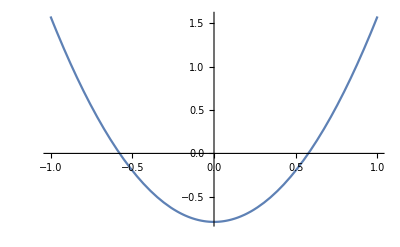

```mathematica
Plot[Evaluate[Table[√((2i+1)/2)LegendreP[i,z],{i,2,2}]],{z,-1,1}]
```

```mathematica
Inverse[({{1, x-2h, (x-2h)^2, (x-2h)^3}, {1, x-h, (x-h)^2, (x-h)^3}, {1, x, x^2, x^3}, {1, x+h, (x+h)^2, (x+h)^3}})].({{Uj2m}, {Uj1m}, {Uj}, {Uj1p}})//FullSimplify
```

{{(6 h^3 Uj-h^2 (3 Uj-6 Uj1m+2 Uj1p+Uj2m) x+3 h (-2 Uj+Uj1m+Uj1p) x^2+(3 Uj-3 Uj1m-Uj1p+Uj2m) x^3)/(6 h^3)},{(h^2 (3 Uj-6 Uj1m+2 Uj1p+Uj2m)+6 h (2 Uj-Uj1m-Uj1p) x+3 (-3 Uj+3 Uj1m+Uj1p-Uj2m) x^2)/(6 h^3)},{(h (-2 Uj+Uj1m+Uj1p)+(3 Uj-3 Uj1m-Uj1p+Uj2m) x)/(2 h^3)},{(-3 Uj+3 Uj1m+Uj1p-Uj2m)/(6 h^3)}}

```mathematica
Solve[({{1, -2h, (-2h)^2, (-2h)^3}, {1, -h, (-h)^2, (-h)^3}, {1, 0, 0, 0}, {1, h, h^2, h^3}}).({{d}, {c}, {b}, {a}})==({{Uj2m}, {Uj1m}, {Uj}, {Uj1p}}),{a, b, c, d}]
```

{{a→-(3 Uj-3 Uj1m-Uj1p+Uj2m)/(6 h^3),b→-(2 Uj-Uj1m-Uj1p)/(2 h^2),c→-(-3 Uj+6 Uj1m-2 Uj1p-Uj2m)/(6 h),d→Uj}}

```mathematica
a=-(3 Uj-3 Uj1m-Uj1p+Uj2m)/(6 h^3);
b=-(2 Uj-Uj1m-Uj1p)/(2 h^2);
c =-(-3 Uj+6 Uj1m-2 Uj1p-Uj2m)/(6 h);
d = Uj;
p[x_]:=a(x - xi)^3+b(x - xi)^2+c(x - xi) + d
```

```mathematica
p''[x]
```

-(2 Uj-Uj1m-Uj1p)/h^2-((3 Uj-3 Uj1m-Uj1p+Uj2m) (x-xi))/h^3

## 4.

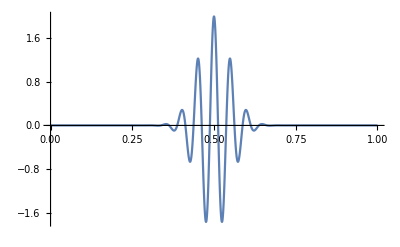

```mathematica
Plot[2 ⅇ^(-200(x  - 1/2)^2)Cos[40π x],{x,0,1},PlotRange->All]
```